```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nnoise=Import["ad_hoc_nnoise_ansatz.csv"];
```

```mathematica
noise=Import["ad_hoc_noise_ansatz.csv"];
```

```mathematica
noise[[2;;,2]]
```

{0.8,0.8,0.8,0.8,0.95,0.85,0.85,0.8,0.95,0.85,0.85,0.92,0.95,0.8,0.8,0.9,0.8,0.81,0.95,0.9,0.92,0.8,0.8,0.8,0.92,0.95,0.9}

```mathematica
StandardDeviation[x]
```

0.0615817

```mathematica
x=noise[[2;;,2]];
y=nnoise[[2;;,2]];
```

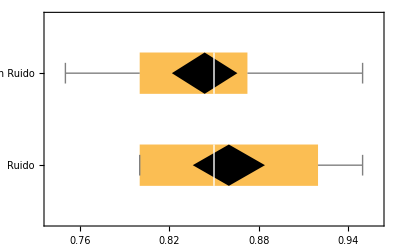

```mathematica
graf=BoxWhiskerChart[{x,y},{"Diamond",{"MeanDiamond",1,Black}},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```

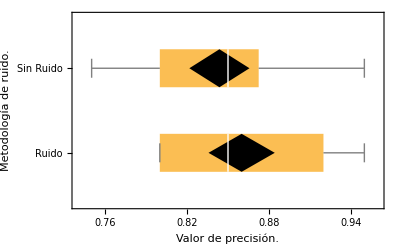

```mathematica
Show[graf,FrameLabel->{{RawBoxes[RowBox[{"Metodología"," ","de"," ",RowBox[{"ruido","."}]}]],None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],HoldForm[Distribución de la ejecución VQC ANSATZ]}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export["distributions_ad_hoc_ansatz.pdf",%]
```

distributions_ad_hoc_ansatz.pdf

```mathematica
With[
{α=0.05,x=noise[[2;;,2]],
y=nnoise[[2;;,2]]},
KolmogorovSmirnovTest[x,y,"TestDataTable", SignificanceLevel->α]]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.185185 | 0.412838

```mathematica
With[
{α=0.05,x=noise[[2;;,2]],
y=nnoise[[2;;,2]]},
SignedRankTest[{x,y}]]
```

0.370745

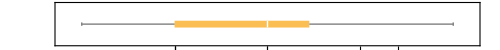

```mathematica
With[{data=nnoise[[2;;,2]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw1=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

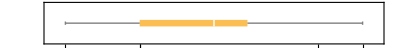

```mathematica
Show[bw1,ImageSize->Full]
```

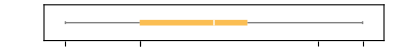

```mathematica
Show[bw1,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Sin ruido)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "distribution_q_ansatz_nnoise.pdf",%]
```

distribution_q_ansatz_nnoise.pdf

```mathematica
SystemOpen["img.pdf"]
```

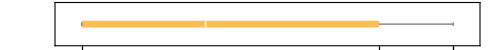

```mathematica
With[{data=noise[[2;;,2]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw2=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

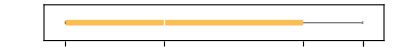

```mathematica
Show[bw2,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Ruido de Pauli)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "distribution_q_ansatz_noise.pdf",%]
```

distribution_q_ansatz_noise.pdf

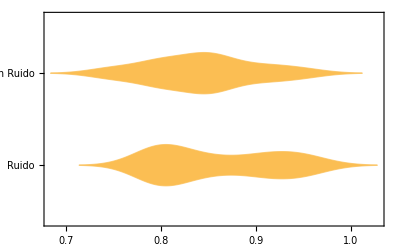

```mathematica
DistributionChart[{x,y},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```